$Aborted

Part::partd: Part specification myTry⟦1⟧ is longer than depth of object.

Part::partd: Part specification myTry⟦2⟧ is longer than depth of object.

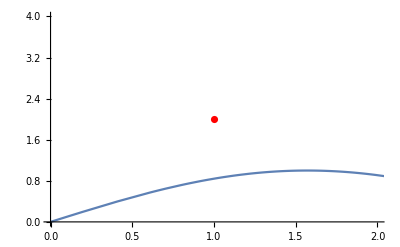

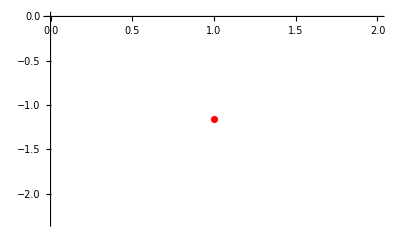

```mathematica
RK45[f_,t0_,T_,h0_,tol_,y0_]:=(

a=List[0,1/4,3/8,12/13,1,1/2];

b={
{0,0,0,0,0,0},
{1/4,0,0,0,0,0},
{3/32,9/32,0,0,0,0},
{1932/2197,-7200/2197,7296/2197,0,0,0},
{439/216,-8,3680/513,-845/4104,0,0},
{-8/27,2,-3544/2565,1859/4104,-11/40,0}
};

p6=List[16/135,0,6656/12825,28561/56430,-9/50,2/55];
p5=List[25/216,0,1408/2565,2197/4104,-1/5,0];
p={p6,p5};

y=List[y0];
t=List[t0];
err=List[0];
tc=t0;
yc=y0;
hc=h0;

While[T≥tc,
k=Table[0,6];

For[s=1,s≤6,s++,
	k[[s]]=hc*f[tc+a[[s]]*hc,yc+b[[s]].k];
];

errc=(p[[1]]-p[[2]]).k;
hnext=hc*Power[tol/Abs[errc],1/5];

If[Abs[errc]>tol,hc=hnext;Continue[],0];

yc=yc+p[[1]].k;
AppendTo[y,yc];
tc=tc+hc;
AppendTo[t,tc];
AppendTo[err,errc];
hc=hnext;
];

res={t,y,err};
res
)



l=1000000;
f[t_,y_]:=l*(-y+Sin[t]);
yr[t_]:=(l*Exp[-l*t]+l^2*Sin[t]-l*Cos[t])/(1+l^2);
T=10;
t0=0;
y0=0;
h0=10^(-12);
tol=10^(-12);

myTry=RK45[f,t0,T,h0,tol,y0];
x=myTry[[1]];
y=myTry[[2]];
n=Length[x];

approxSol=ListPlot[Table[{x[[k]],y[[k]]},{k,1,n}],PlotStyle->Red];
realSol=Plot[yr[xt],{xt,t0,T}];
Print[Show[approxSol,realSol]];
ListPlot[Table[{x[[k]],yr[x[[k]]]-y[[k]]},{k,1,n}],PlotStyle->Red]
```